## Numerical results for trophical transmission model with multiple infections

```mathematica
SetDirectory[NotebookDirectory[]]
<<Tools`
ParallelNeeds["Tools`"](* Import package Tools that define useful functions*)
```

/Users/phuongnguyen/Work/multipleinfections/code

# ODEs

```mathematica
dIsdt = R[Iw, Is, Iww]- d Is- Πs[Ds, Dw, Dww] Is  - ηw  Is ;
dIwdt =  (1-p)ηw Is  - (d + αw)Iw - Πw[Ds, Dw,Dww, βw]Iw; 
dIwwdt =  p ηw Is  - (d + αww)Iww - Πww[Ds, Dw, Dww,βww]Iww; 
dDsdt =B[Ds, Dw,Dww, Is, Iw, Iww]  - μ Ds - (λww + λw) Ds;
dDwdt =(λw + 2(1-q)λww) Ds- (μ + σw) Dw - (2(1-q)λww +λw)Dw;
dDwwdt = q λww Ds + (2(1-q)λww + λw)Dw - (μ + σww)Dww;
dWdt = fw Dw +fww Dww- δ W - ηw Is;

forceInf = {ηw -> γ W, λw -> βw Iw, λww -> βww Iww};
odesRes = {dIsdt, dIwdt, dIwwdt, dDsdt, dDwdt, dDwwdt, dWdt};
varRes = {Is, Iw, Iww, Ds, Dw, Dww, W};
vartRes = {Is[t], Iw[t], Iww[t], Ds[t], Dw[t], Dww[t], W[t]};
```

# Reproduction ratio R0

```mathematica
R0ww = Is γ (p  q βww)/(d+αww+Πww[Ds, Dw, Dww,βww]) Ds/(μ+σww)fww/(Is γ+δ);
R0w = Is γ (((1-p) βw)/(d+αw+ Πw[Ds, Dw,Dww, βw])+(2 p (1-q)  βww)/(d+αww+Πww[Ds, Dw, Dww,βww]))Ds/( βw Iw-2 (-1+q)  βww Iww+μ+σw)fw/(Is γ+δ);
R0 = R0ww  + R0w;
```

# Graph format and parallel computation

```mathematica
includeFrame = True(*{{True, False}, {True,False}}*);
imageSize = 600;
frameStyle = Directive[Black,Thickness[0.003]];
labelStyle = {Black, FontSize-> 24};
colorlist = ColorData[97,"ColorList"]
colorstable = ColorData[97,"ColorList"][[{1, 2, -2}]]
ihostCol = ColorData[97,"ColorList"][[1]];
 dhostCol = ColorData[97,"ColorList"][[4]];
fCol1 = ColorData[97,"ColorList"][[3]];
fCol2 = ColorData[97,"ColorList"][[-1]];
pointsize = 0.02;
figResolution = 300;
colbifur = {Black, Darker[Gray], Gray};
colbifurfilling = {Lighter[Gray, 0.1], Lighter[Gray, 0.5], Lighter[Gray, 0.8]};
panellabel = 550;
```

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.571589, 0.586483, 0.],RGBColor[0.915, 0.3325, 0.2125],RGBColor[0.40082222609352647, 0.5220066643438841, 0.85],RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142],RGBColor[0.736782672705901, 0.358, 0.5030266573755369],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]}

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.736782672705901, 0.358, 0.5030266573755369]}

# Linear birth function for intermediate host

```mathematica
func0 = {R[Iw, Is, Iww] -> r(Is + Iw+Iww), Πs[Ds, Dw, Dww]-> ρ(Ds +Dw + Dww), Πw[Ds, Dw,Dww, βw]->  βw(Ds + Dw+Dww),Πww[Ds, Dw,Dww, βww]->  βww(Ds + Dw+Dww), B[Ds, Dw,Dww, Is, Iw, Iww]-> ρ c (Ds + Dw + Dww)(Is + Iw+Iww)};
sysfunc0 = odesRes/.forceInf/.func0;
sysNDSolvefunc0 = MakeSystem[varRes, t,sysfunc0];
```

## Jacobian matrix

```mathematica
Jmatfunc0 = D[sysfunc0, {varRes}];
```

## Ecological trajectories

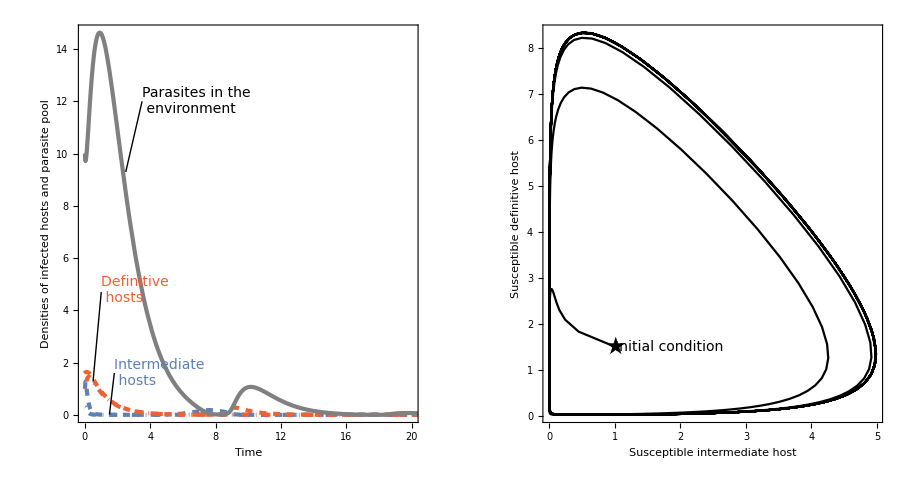

```mathematica
prEco0 = {ρ -> 1.2, d -> 0.9,r -> 2.5, γ -> 2.9, αw-> 0, αww-> 0, βw-> 1.5, βww-> 1.5,p-> 0.1, c-> 1.4, μ-> 0.9, σw-> 0,σww-> 0,q-> 0.01, fw -> 6.5,fww-> 7.5, δ-> 0.9};

maxt = 100;

init0= {Is[0]== 1, Iw[0] == 1,Iww[0]==0.3, Ds[0] ==1.5, Dw[0] == 1.7,Dww[0]==1, W[0] == 10};

sols0 = NSolve[Thread[(odesRes/.func0/.forceInf/.prEco0) == 0], varRes];
ndsol0 = NDSolve[Join[sysNDSolvefunc0/.prEco0, init0], varRes, {t, 0, maxt}] ;

range = {{-1, 20},{-1, 20}};
trajectStyle = {{ihostCol, Dashed,Thickness[0.005]}, {ihostCol, DotDashed,Thickness[0.005]}, {dhostCol, Dashed,Thickness[0.005]}, {dhostCol, DotDashed,Thickness[0.005]}, {Gray, Thickness[0.005]}};
epilogParasite0 = {{Black, Line[{{2.5, 9.3}, {3.5, 12}}]}, {Black, Line[{{0.5, 1.3}, {1., 4.7}}]}, {Black, Line[{{1.5, 0.01}, {1.8, 1.6}}]}, {Black, Text[Style["Parasites in the \n environment", FontSize->14], {3.5, 12}, {-1.05, 0}]}, {ihostCol, Text[Style["Intermediate \n hosts", FontSize->14], {1.8, 1.6}, {-0.5, 0}]}, {dhostCol, Text[Style["Definitive \n hosts", FontSize->14], {1, 4.2}, {-0.5, -1}]}};
p1 = Plot[Evaluate[{Iw[t], Iww[t], Dw[t], Dww[t],W[t]}/.ndsol0], {t, 0, maxt}, AspectRatio->1,PlotRange-> {{0, 20}, All}, FrameLabel->{Style["Time",Black,24],Style["Densities of infected hosts\n and parasite pool",Black,24]}, ImageSize->imageSize, Frame-> True,FrameStyle->frameStyle,LabelStyle->labelStyle,PlotStyle->trajectStyle, Epilog->epilogParasite0];


epilogHost0 = {{Black, Text[Style[★, FontSize->24], {1., 1.5}, {0, 0}]}, {Black, Text[Style["Initial condition", FontSize->14], {1., 1.5}, {-1.3, -0.2}]}};
p2 = ParametricPlot[{Evaluate[{Is[t], Ds[t]}/.ndsol0]}, {t, 0, maxt}, AspectRatio->1, PlotRange->All, Frame->includeFrame, PlotStyle->Black, FrameStyle->frameStyle, FrameLabel->{Style["Susceptible intermediate host",Black,24], Style["Susceptible definitive host",Black,24]}, ImageSize->imageSize, LabelStyle->labelStyle, Epilog->epilogHost0];

GraphicsRow[{p1, p2}, ImageSize->{900, 500}]
(*Export["diseasefree_linear.pdf",%, ImageResolution-> figResolution]*)
```

# Nonlinear birth function for intermediate host

```mathematica
func1 = {R[Iw, Is, Iww] -> r(1-k(Is + Iw+Iww))(Is + Iw+Iww), Πs[Ds, Dw, Dww]-> ρ(Ds +Dw + Dww), Πw[Ds, Dw,Dww, βw]->  (ρ +βw)(Ds + Dw+ Dww),Πww[Ds, Dw, Dww, βww]->  (ρ+βww)(Ds + Dw+Dww), B[Ds, Dw,Dww, Is, Iw, Iww]-> ρ c (Ds + Dw + Dww)(Is + Iw+Iww)};

sysfunc1 = odesRes/.forceInf/.func1;
sysNDSolvefunc1 = MakeSystem[varRes, t, sysfunc1];
```

## Jacobian matrix

```mathematica
Jmatfunc1 = D[sysfunc1, {varRes}];
```

## Ecological trajectories

## Disease free equilibrium

```mathematica
prEcoNL = {ρ -> 1.2, d -> 0.9,r -> 2.5, γ -> 2.9, αw-> 0, αww-> 0, βw-> 1.5, βww-> 1.5,p-> 0.1, c-> 1.4, μ-> 3.9, σw-> 0,σww-> 0,q-> 0.01, fw -> 7.5,fww-> 7.5, δ-> 0.9, k -> 0.26};

maxt = 100;

solsNL = NSolve[Thread[(sysfunc1/.prEcoNL) == 0], varRes];
range1 = { {-0.05, 2.4}, {-0.05, 0.7}};
{Is[0]== 1.2, Iw[0] == 0.2,Iww[0]==0.3, Ds[0] ==0.5, Dw[0] == 0.7,Dww[0]==0.1, W[0] == 0.8};
ndsolNL = NDSolve[Join[sysNDSolvefunc1/.prEcoNL, %], varRes, {t, 0, maxt}] ;

ieq1 = Evaluate[Is[maxt]/.ndsolNL][[1]];
deq1 = Evaluate[Ds[maxt]/.ndsolNL][[1]];

epilogHost1 = {{Black, PointSize[pointsize],Point[{{ieq1, deq1}}]}, {Black, Text[Style[★, FontSize->24], {1.2, 0.5}, {0, 0}]}, {Black, Text[Style["Initial condition", FontSize->14], {1.2, 0.5}, {-1.2, -0.2}]}, {Black, Text[Style["Equilibrium", FontSize->14], {ieq1, deq1}, {1.2, -0.2}]}};
ppHost1 = ParametricPlot[Evaluate[{Is[t], Ds[t]}/.ndsolNL], {t, 0, maxt}, AspectRatio->1, Frame->includeFrame, PlotStyle->Black, FrameStyle -> frameStyle, PlotRange->range1, FrameLabel->{"Susceptible intermediate host", "Susceptible definitive host"}, LabelStyle->labelStyle,   ImageSize->imageSize,Epilog-> epilogHost1, PlotLabel->Pane["B)", Alignment->Left, ImageSize->panellabel]];

epilogParas1 = {{Black, Line[{{0.5, 1}, {2, 1.1}}]}, {Black, Line[{{3.2, 0.18}, {5, 0.2}, {3.1, 0.025}}]}, {Black, Line[{{1.5, 0.01}, {2, 0.6}}]}, {Black, Text[Style["Parasites in the \n environment", FontSize->14], {2, 1.1}, {-1.05, 0}]}, {ihostCol, Text[Style["Intermediate \n hosts", FontSize->14], {5, 0.2}, {-1.05, 0}]}, {dhostCol, Text[Style["Definitive \n hosts", FontSize->14], {2, 0.6}, {-1.05, 0}]}};
trajectStyle = {{ihostCol, Dashed}, {ihostCol, DotDashed}, {dhostCol, Dashed}, {dhostCol, DotDashed}, {Gray}};
ppParasite1 = Plot[Evaluate[{Iw[t], Iww[t], Dw[t], Dww[t], W[t]}/.ndsolNL], {t, 0, maxt}, AspectRatio->1,PlotRange->{{0, 10}, {-0.1, 1.2}}, PlotStyle->trajectStyle, Frame->includeFrame, LabelStyle->labelStyle, ImageSize->imageSize, FrameStyle->frameStyle, FrameLabel->{"Time", "Density of infected host \n and parasite pool"}, Epilog->epilogParas1, PlotLabel->Pane["A)", Alignment->Left, ImageSize->panellabel]];
```

## Disease stable equilibrium

```mathematica
prEcoDSNL = {ρ -> 1.2, d -> 0.9,r -> 2.5, γ -> 2.9, α-> 0, βw-> 4.5, βww-> 4.5,p-> 0.1, c-> 1.4, μ-> 3.9, σ-> 0,q-> 0.01, fw -> 45, fww-> 45,δ-> 0.9, k -> 0.26};



condsimplifyNL = {αw-> α, αww-> α, σw-> σ, σww-> σ};

maxt =30;

range2 = {{-0.05, 2.3}, {-0.01, 0.12}};
{Is[0]== 0.15, Iw[0] == 0.5,Iww[0]==0.2, Ds[0] ==0.1, Dw[0] == 0.1,Dww[0]==0.01, W[0] == 0.01};
ndsolDS = NDSolve[Join[sysNDSolvefunc1/.condsimplifyNL/.prEcoDSNL, %], varRes, {t, 0, maxt}] ;

ieq2 = Evaluate[Is[maxt]/.ndsolDS][[1]];
deq2 = Evaluate[Ds[maxt]/.ndsolDS][[1]];
epilogHost2 = {{Black, PointSize[pointsize],Point[{{ieq2, deq2}}]}, {Black, Text[Style[★, FontSize->24], {0.15, 0.1}, {0, 0}]}, {Black, Text[Style["Initial condition", FontSize->14], {0.15, 0.1}, {-1.2, -0.2}]}, {Black, Text[Style["Equilibrium", FontSize->14], {ieq2, deq2}, {-1.2, -0.2}]}};
ppHost2 = ParametricPlot[Evaluate[{Is[t], Ds[t]}/.ndsolDS], {t, 0, maxt},  Frame->includeFrame,AspectRatio->1, PlotStyle->Black, FrameStyle -> frameStyle, PlotRange->range2, FrameLabel->{"Susceptible intermediate host", "Susceptible definitive host"}, LabelStyle->labelStyle, ImageSize->imageSize, Epilog->epilogHost2, PlotLabel->Pane["D)", Alignment->Left, ImageSize->panellabel]];

epilogParas2 = {{Black, Line[{{0.7, 1}, {3, 1.1}}]}, {Black, Line[{{10, 0.07}, {15, 0.5}, {10, 0.48}}]}, {Black, Line[{{20, 0.01}, {23, 0.4}}]}, {Black, Text[Style["Parasites in the \n environment", FontSize->14], {2, 1.1}, {-1.05, 0}]}, {ihostCol, Text[Style["Intermediate \n hosts", FontSize->14], {15, 0.5}, {-1.05, 0}]}, {dhostCol, Text[Style["Definitive \n hosts", FontSize->14], {23, 0.4}, {-1.05, 0}]}};
trajectStyle = {{ihostCol, Dashed}, {ihostCol, DotDashed}, {dhostCol, Dashed}, {dhostCol, DotDashed}, {Gray, Thick}};
ppParasite2 = Plot[Evaluate[{Iw[t], Iww[t], Dw[t], Dww[t], W[t]}/.ndsolDS], {t, 0, maxt}, AspectRatio->1, PlotRange->{{-0.2, maxt}, {-0.05, 1.2}}, PlotStyle->trajectStyle, Frame-> includeFrame, FrameStyle->frameStyle, FrameLabel->{"Time", "Density of infected host \n and parasite pool"}, LabelStyle->labelStyle, ImageSize->imageSize, Epilog->epilogParas2, PlotLabel->Pane["C)", Alignment->Left, ImageSize->panellabel]];
```

## Combined disease free and disease stable ecology plot

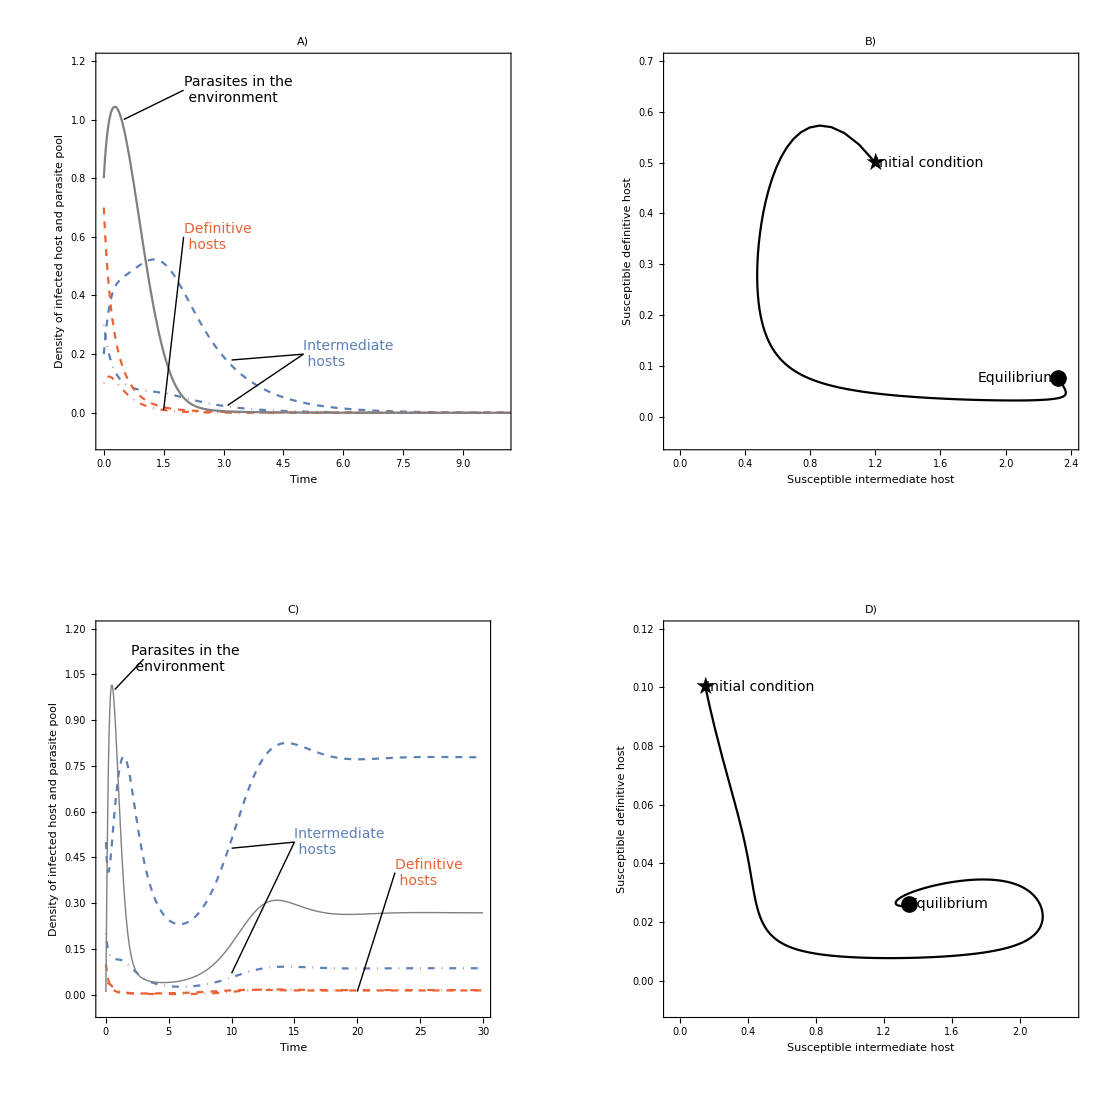

```mathematica
GraphicsGrid[{{ppParasite1, ppHost1}, {ppParasite2, ppHost2}}, ImageSize->{1100, 1100}]
(*Export["ecotraject_nonlinear.pdf", %, ImageResolution-> figResolution]*)
```

## Bifurcation f_w (f_ww = ϵ f_w)

## Parameter set 1

CALCULATE

```mathematica
parfw = {ρ -> 1.2, d -> 0.9,r -> 2.5, γ -> 2.9, αw-> 0,αww-> 0, βw-> 1.5, βww-> 1.5,p-> 0.1, c-> 1.4, μ-> 3.9, σw-> 0,σww-> 0,q-> 0.01, δ-> 0.9, k -> 0.26, ϵ-> 4};
fwstart = 27;
fwend = 70;
fwstep = 0.7;
fwrange = Range[fwstart, fwend, fwstep];

(*Find all solutions of the system with the given parameter values*)
solsfwAll1 = NSolve[Thread[(odesRes/.func1/.forceInf/.fww-> ϵ fw/.parfw/.fw-> 36) == 0], varRes, Reals];

(*Select disease circulation solutions*)
fwAllPositive1= ParallelTable[NSolvePositive[sysfunc1/.fww-> ϵ fw, parfw, fw -> i, varRes, eq], {i, fwstart, fwend, fwstep}];
(*Select disease free solutions*)
solsfwzero1 = Select[solsfwAll1, (Is/.#)> 0 &&(Iw/.#)== 0 &&(Iww/.#)== 0&&(Ds/.#)>0 &&(Dw/.#)== 0 &&(Dww/.#)== 0 &&(W/.#)== 0 &][[1]];
```

PLOT

```mathematica
fwlist = fw/.Flatten[fwAllPositive1, 1];
eqfwlist = eq/.Flatten[fwAllPositive1, 1];
eqfwzero = ConstantArray[solsfwzero1, Length[fwrange]];

rangeIw = {{fwstart, fwend}, {-0.1, 2.5}};
rangeDw = {{fwstart, fwend}, {-0.001, 0.02}};

Iwfwlist = Iw/.eqfwlist;

sdat1 = MakeListPlotData[fwlist, Iwfwlist];
markers1 = ListStableMark[Jmatfunc1/.fww-> ϵ fw, parfw, fw, fwlist, eqfwlist, { "✶","○", "●" }];

zdat1 = MakeListPlotData[fwrange, Iw/.eqfwzero];
markerz1 = ListStableMark[Jmatfunc1/.fww-> ϵ fw, parfw, fw, fwrange, eqfwzero, { "✶","○", "●" }];

pIw = ListPlot[Join[sdat1, zdat1], PlotMarkers->Join[markers1, markerz1], PlotStyle->Black , PlotRange->rangeIw, ImageSize->imageSize, Frame->includeFrame, FrameLabel->{" Parasite reproduction \n in single infection", "Density of singly infected \n intermediate host"},LabelStyle->labelStyle,FrameStyle->frameStyle, PlotLabel->Pane["C)", Alignment->Left, ImageSize->panellabel]];

Dwfwlist = Dw/.eqfwlist;
sdat2 = MakeListPlotData[fwlist, Dwfwlist];
markers2 = ListStableMark[Jmatfunc1/.fww-> ϵ fw, parfw, fw, fwlist, eqfwlist, { "✶","○", "●" }];

zdat2 = MakeListPlotData[fwrange, Dw/.eqfwzero];
markerz2 = ListStableMark[Jmatfunc1/.fww-> ϵ fw, parfw, fw, fwrange, eqfwzero, { "✶","○", "●" }];

pDw = ListPlot[Join[sdat2, zdat2], PlotMarkers->Join[markers2, markerz2], PlotStyle->Black , PlotRange->rangeDw, ImageSize->imageSize, Frame->includeFrame, FrameLabel->{" Parasite reproduction \n in single infection", "Density of singly infected \n definitive host"},LabelStyle->labelStyle,FrameStyle->frameStyle, PlotLabel->Pane["D)", Alignment->Left, ImageSize->panellabel]];
```

## Parameter set 2

CALCULATION

```mathematica
parfw = {ρ -> 1.2, d -> 0.9,r -> 2.5, γ -> 2.9, αw-> 0,αww-> 0, βw-> 1.5, βww-> 1.5,p-> 0.1, c-> 1.4, μ-> 3.9, σw-> 0,σww-> 0,q-> 0.01, δ-> 0.9, k -> 0.26, ϵ-> 1};

fwstart = 27;
fwend = 70;
fwstep = 0.7;
fwrange = Range[fwstart, fwend, fwstep];

(*Find all solutions of the system with the given parameter values*)
solsfwAll2 = NSolve[Thread[(odesRes/.func1/.forceInf/.fww-> ϵ fw/.parfw/.fw-> 40.5) == 0], varRes, Reals];

(*Select disease circulation solutions*)
solsfw2= Select[solsfwAll2, (Is/.#)> 0 &&(Iw/.#)> 0 &&(Iww/.#)> 0 &&(W/.#)> 0 &][[1]];

(*Select disease free solutions*)
solsfwzero2 = Select[solsfwAll2, (Is/.#)> 0 &&(Iw/.#)== 0 &&(Iww/.#)== 0&&(Ds/.#)>0 &&(Dw/.#)== 0 &&(Dww/.#)== 0 &&(W/.#)== 0 &][[1]];

(*Select disease circulation solutions*)
fwAllPositive2= ParallelTable[NSolvePositive[sysfunc1/.fww-> ϵ fw, parfw, fw -> i, varRes, eq], {i, fwstart, fwend, fwstep}];
```

PLOTTING

```mathematica
rangeIw = {{fwstart, fwend}, {-0.1, 1.2}};
rangeDw = {{fwstart, fwend}, {-0.001, 0.02}};
fwlist = fw/.Flatten[fwAllPositive2, 1];
eqfwlist = eq/.Flatten[fwAllPositive2, 1];
eqfwzero = ConstantArray[solsfwzero2, Length[fwrange]];

Iwfwlist = Iw/.eqfwlist;

sdat3 = MakeListPlotData[fwlist, Iwfwlist];
markers3 = ListStableMark[Jmatfunc1/.fww-> ϵ fw, parfw, fw, fwlist, eqfwlist, { "✶","○", "●" }];
zdat3 = MakeListPlotData[fwrange, Iw/.eqfwzero];
markerz3 = ListStableMark[Jmatfunc1/.fww-> ϵ fw, parfw, fw, fwrange, eqfwzero, { "✶","○", "●" }];

ppIw = ListPlot[Join[sdat3, zdat3], PlotMarkers->Join[markers3, markerz3], PlotStyle->Black , PlotRange->rangeIw, ImageSize->imageSize, Frame->includeFrame, FrameLabel->{" ", "Density of singly infected \n definitive host"},LabelStyle->labelStyle,FrameStyle->frameStyle, PlotLabel->Pane["A)", Alignment->Left, ImageSize->panellabel]];

Dwfwlist = Dw/.eqfwlist;
sdat4 = MakeListPlotData[fwlist, Dwfwlist];
markers4 = ListStableMark[Jmatfunc1/.fww-> ϵ fw, parfw, fw, fwlist, eqfwlist, { "✶","○", "●" }];

zdat4 = MakeListPlotData[fwrange, Dw/.eqfwzero];
markerz4 = ListStableMark[Jmatfunc1/.fww-> ϵ fw, parfw, fw, fwrange, eqfwzero, { "✶","○", "●" }];

ppDw = ListPlot[Join[sdat4, zdat4], PlotMarkers->Join[markers4, markerz4], PlotStyle->Black , PlotRange->rangeDw, ImageSize->imageSize, Frame->includeFrame, FrameLabel->{" ", "Density of singly infected \n definitive host"},LabelStyle->labelStyle,FrameStyle->frameStyle, PlotLabel->Pane["B)", Alignment->Left, ImageSize->panellabel]];
```

## Combined plot parameter set 1 and parameter set 2

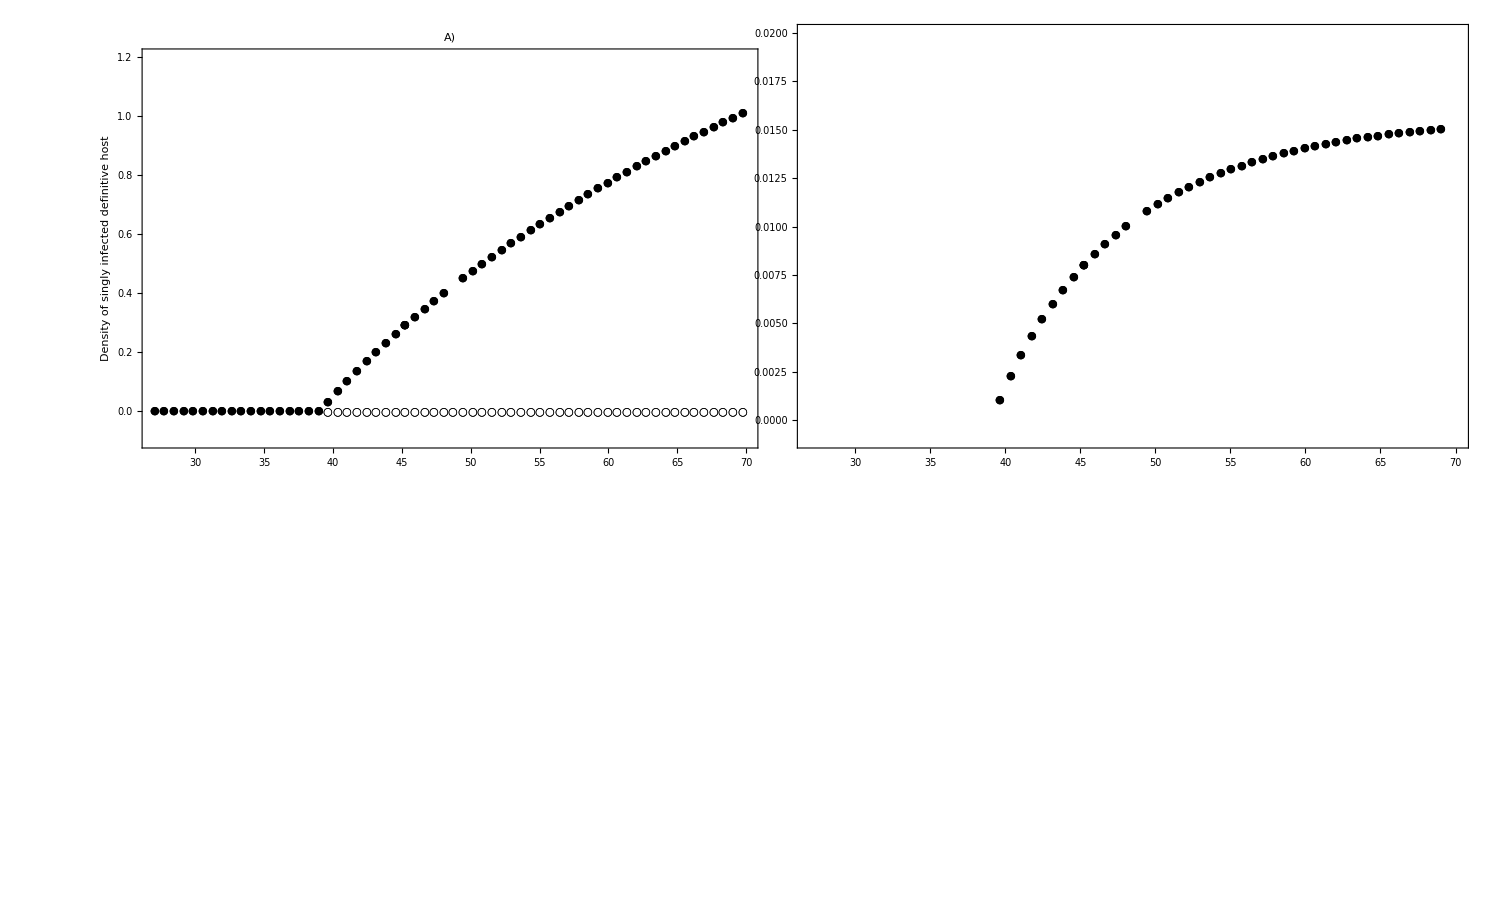

```mathematica
GraphicsGrid[{{ppIw, ppDw}, {pIw, pDw}}, ImageSize->{1500, 900}, Spacings-> -60]
(*Export["bistability.pdf", %, ImageResolution-> figResolution]*)
```

## Bifurcation ϵ and f_w (f_ww = ϵ f_w)

CALCULATE

```mathematica
parϵfw = {ρ -> 1.2, d -> 0.9,r -> 2.5, γ -> 2.9, αw-> 0,αww-> 0, βw-> 1.5, βww-> 1.5,p-> 0.1, c-> 1.4, μ-> 3.9, σw-> 0,σww-> 0,q-> 0.01, δ-> 0.9, k -> 0.26};

ϵstart = 0;
ϵend = 6;
ϵinterval = 0.5;
fwstart = 36;
fwend = 42;
fwinterval = 0.5;

ϵfwAllresults = ParallelTable[NSolveCodim2Positive[sysfunc1/.fww-> ϵ fw, parϵfw, {ϵ -> i}, {fw-> j}, ϵfw, eq,varRes,15],{i, ϵstart, ϵend, ϵinterval}, {j, fwstart, fwend, fwinterval}];
```

PLOT

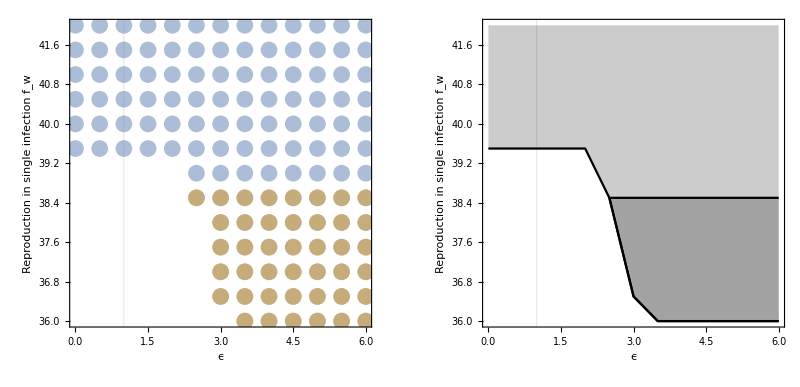

```mathematica
eqϵfw =eq/. Flatten[ϵfwAllresults, 2];
ϵfwlist = ϵfw/.Flatten[ϵfwAllresults, 2];
rangeϵfw= {{ϵstart , ϵend}, {fwstart , fwend}};

marklist = ListStableMarkTwoParameters[Jmatfunc1/.fww-> ϵ fw, parϵfw,{ϵ, fw}, ϵfwlist, eqϵfw, colorstable, True];
MakeListPlotData[ϵfwlist[[All, 1]], ϵfwlist[[All, 2]]];
p0 = ListPlot[%,  PlotStyle->marklist, PlotRange->rangeϵfw, ImageSize->imageSize, Frame-> includeFrame, FrameLabel->{"ϵ", "Reproduction in single infection f_w"}, GridLines->{{1},{}}, GridLinesStyle-> {Thick,Black}, LabelStyle->labelStyle,FrameStyle->frameStyle,AspectRatio->1];
GetBoundaryLineBiStable[ϵfwlist];
p1 =ListLinePlot[%, AspectRatio->1, PlotRange->rangeϵfw, Frame->includeFrame, FrameStyle->frameStyle, FrameLabel->{"ϵ", "Reproduction in single infection f_w"}, LabelStyle->labelStyle,GridLines->{{1},{}}, GridLinesStyle-> {Thick,Black}, PlotStyle-> Black, Filling-> {1-> {2}}];
GetBoundaryLineSingle[ϵfwlist];
p2 = ListLinePlot[%, AspectRatio->1, PlotRange->rangeϵfw, Frame->includeFrame, FrameStyle->frameStyle, PlotStyle-> Black, Filling->Top];
GraphicsGrid[{{p0, Show[{p1, p2}]}}]
```

## Bifurcation of single and double infection (β_w and β_ww) setting f_ww=ϵ f_w

```mathematica
thick = 0.003;
βwstart = 0;
βwend = 2.5;
βwstep = 0.05;
βwwstart = 0;
βwwend = 17;
βwwstep = 0.3;
range= {{βwstart, βwend}, {βwwstart, βwwend}};
```

## Parameter set 1 (f_ww=f_w)

CALCULATE

```mathematica
parmanip1 = {ρ -> 1.2, d -> 0.9,r -> 2.5, γ -> 2.9, αw-> 0,αww-> 0, p-> 0.1, c-> 1.4, μ-> 3.9, σw-> 0,σww-> 0,q-> 0.01, δ-> 0.9, k -> 0.26, ϵ-> 1, fw -> 40};


manipAllResults1 = ParallelTable[NSolveCodim2Positive[sysfunc1/.fww-> ϵ fw, parmanip1, {βw -> x}, {βww-> y}, β, eq,varRes, 15],{x, βwstart, βwend, βwstep}, {y, βwwstart, βwwend, βwwstep}];
```

NSolve::sfail: Subsystem could not be solved for (172209 Ds)/183067-(117425 Dw)/183067-(116690 Dww)/183067-(138285 Is)/183067+(169206 Iw)/183067-(151916 Iww)/183067-(185189 W)/183067 at value 5.1143585177348115774. The likely cause is failure to detect zero due to low precision. The likely effect is the loss of one or more solutions. Increasing WorkingPrecision might prevent some solutions from being lost.

NSolve::sfail: Subsystem could not be solved for (172209 Ds)/183067-(117425 Dw)/183067-(116690 Dww)/183067-(138285 Is)/183067+(169206 Iw)/183067-(151916 Iww)/183067-(185189 W)/183067 at value 13.30801804213207+0. ⅈ. The likely cause is failure to detect zero due to low precision. The likely effect is the loss of one or more solutions. Increasing WorkingPrecision might prevent some solutions from being lost.

NSolve::sfail: Subsystem could not be solved for (172209 Ds)/183067-(117425 Dw)/183067-(116690 Dww)/183067-(138285 Is)/183067+(169206 Iw)/183067-(151916 Iww)/183067-(185189 W)/183067 at value 0.7807656160179472. The likely cause is failure to detect zero due to low precision. The likely effect is the loss of one or more solutions. Increasing WorkingPrecision might prevent some solutions from being lost.

NSolve::sfail: Subsystem could not be solved for (172209 Ds)/183067-(117425 Dw)/183067-(116690 Dww)/183067-(138285 Is)/183067+(169206 Iw)/183067-(151916 Iww)/183067-(185189 W)/183067 at value 12.7211866239475747. The likely cause is failure to detect zero due to low precision. The likely effect is the loss of one or more solutions. Increasing WorkingPrecision might prevent some solutions from being lost.

NSolve::sfail: Subsystem could not be solved for (172209 Ds)/183067-(117425 Dw)/183067-(116690 Dww)/183067-(138285 Is)/183067+(169206 Iw)/183067-(151916 Iww)/183067-(185189 W)/183067 at value 13.00491440565147972+0. ⅈ. The likely cause is failure to detect zero due to low precision. The likely effect is the loss of one or more solutions. Increasing WorkingPrecision might prevent some solutions from being lost.

NSolve::sfail: Subsystem could not be solved for (172209 Ds)/183067-(117425 Dw)/183067-(116690 Dww)/183067-(138285 Is)/183067+(169206 Iw)/183067-(151916 Iww)/183067-(185189 W)/183067 at value -1.85936587589079041. The likely cause is failure to detect zero due to low precision. The likely effect is the loss of one or more solutions. Increasing WorkingPrecision might prevent some solutions from being lost.

General::stop: Further output of NSolve::sfail will be suppressed during this calculation.

NSolve::sfail: Subsystem could not be solved for (172209 Ds)/183067-(117425 Dw)/183067-(116690 Dww)/183067-(138285 Is)/183067+(169206 Iw)/183067-(151916 Iww)/183067-(185189 W)/183067 at value -1.9253142044304434. The likely cause is failure to detect zero due to low precision. The likely effect is the loss of one or more solutions. Increasing WorkingPrecision might prevent some solutions from being lost.

NSolve::sfail: Subsystem could not be solved for (172209 Ds)/183067-(117425 Dw)/183067-(116690 Dww)/183067-(138285 Is)/183067+(169206 Iw)/183067-(151916 Iww)/183067-(185189 W)/183067 at value -143.399498349228282+0. ⅈ. The likely cause is failure to detect zero due to low precision. The likely effect is the loss of one or more solutions. Increasing WorkingPrecision might prevent some solutions from being lost.

General::stop: Further output of NSolve::sfail will be suppressed during this calculation.

PLOT

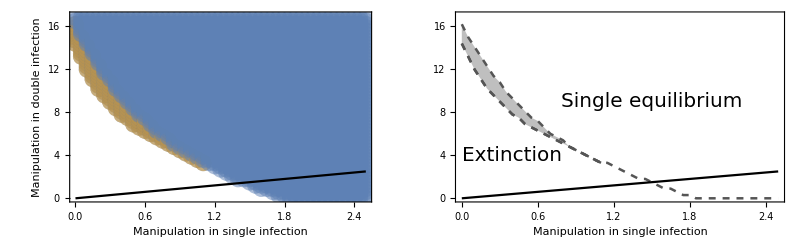

```mathematica
equilibrium =eq/. Flatten[manipAllResults1 , 2];
parslist = β/.Flatten[manipAllResults1, 2];
marklist = ListStableMarkTwoParameters[Jmatfunc1/.fww-> ϵ fw, parmanip1,{βw, βww}, parslist, equilibrium, colorstable, True];
MakeListPlotData[parslist[[All, 1]], parslist[[All, 2]]];
p0 = ListPlot[%,  PlotStyle->marklist, PlotRange->range, ImageSize->imageSize, Frame-> includeFrame, FrameLabel->{"Manipulation in single infection", "Manipulation in double infection"}, LabelStyle->labelStyle, ImageSize->imageSize];
p1 = Plot[x, {x, βwstart, βwend}, PlotStyle-> Black, ImageSize->imageSize];
pp2 = Show[{p0, p1}];
GetBoundaryLineBiStable[parslist];
lp1 =ListLinePlot[%,  PlotRange->range, Frame->includeFrame, FrameStyle->frameStyle, FrameLabel->{"Manipulation in single infection", ""}, LabelStyle->labelStyle, PlotStyle->  {{Dashed, Thickness[thick], colbifur[[2]]},{Dashed,Thickness[thick], colbifur[[2]]}}, Filling-> {1-> {2}}, FillingStyle->colbifurfilling[[2]],ImageSize->imageSize, Epilog-> {Text[Style["Extinction", FontSize->20], {0.4, 4}], Text[Style["Single equilibrium", FontSize->20], {1.5, 9}]}];
GetBoundaryLineSingle[parslist];
lp2= ListLinePlot[%, PlotRange->range, Frame->includeFrame, FrameStyle->frameStyle, LabelStyle->labelStyle, PlotStyle-> {Dashed, Thickness[thick], colbifur[[2]]}, ImageSize->imageSize];
l21 = Show[{lp1,lp2, p1}];
GraphicsGrid[{{pp2, l21}}]
```

## Contour Plot for Reproduction ratio

### Reproduction ratio

```mathematica
R0func1 = R0/.func1/.Dw -> 0/.Dww-> 0/.Iw-> 0/.Iww-> 0//Simplify;
```

### Plot

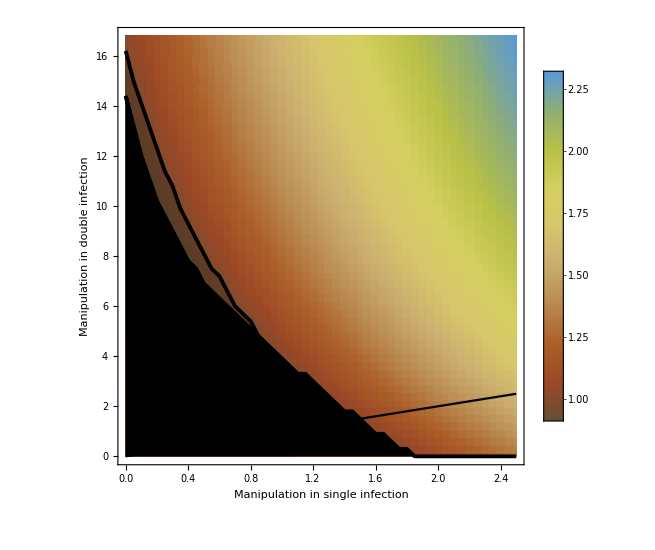

```mathematica
thickR0 = 0.005;
Thread[sysfunc1==0]/.{Iw-> 0, Iww-> 0, Dw-> 0, Dww-> 0, W-> 0};
diseasefree = Solve[%, {Is, Ds}][[3]];
R0func1/.{Iw -> 0, Iww->0, Dw-> 0, Dww->0 , W-> 0}/.diseasefree/.fww-> ϵ fw/.parmanip1/. Thread[{Thread[βw->parslist[[All, 1]]],Thread[βww-> parslist[[All, 2]]]}];
Join[parslist, Partition[%, 1], 2];
(* Plot R0*)R0g = ListDensityPlot[%, PlotLegends->Automatic, Frame-> includeFrame, FrameStyle->frameStyle, LabelStyle->labelStyle, FrameLabel->{"Manipulation in single infection", "Manipulation in double infection"}, ImageSize->imageSize, ColorFunction->"SouthwestColors",   PlotLegends->Automatic,InterpolationOrder->0];

(* Plot Subscript[β, w] = Subscript[β, ww] line*)
p0 = Plot[x, {x, βwstart, βwend}, PlotStyle-> Black, ImageSize->imageSize];

(* Plot bistability area*)
equilibrium =eq/. Flatten[manipAllResults1 , 2];
parslist = β/.Flatten[manipAllResults1, 2];
marklist = ListStableMarkTwoParameters[Jmatfunc1/.fww-> ϵ fw, parmanip1,{βw, βww}, parslist, equilibrium, colorstable, True];
MakeListPlotData[parslist[[All, 1]], parslist[[All, 2]]];
GetBoundaryLineBiStable[parslist];
p1 =ListLinePlot[%,  PlotRange->range, Frame->includeFrame, FrameStyle->frameStyle, FrameLabel->{"Manipulation in single infection", "Manipulation in double infection"}, LabelStyle->labelStyle, PlotStyle->  {{Thickness[thickR0], Black},{Thickness[thickR0],Black}}, Filling-> {{1-> {2}}, {1-> Axis}},FillingStyle->{HatchFilling[],PatternFilling[{"Halftone",Gray},ImageScaled[1/80]] },ImageSize->imageSize];
GetBoundaryLineSingle[parslist];
p2= ListLinePlot[%,  PlotRange->range, Frame->includeFrame, FrameStyle->frameStyle, LabelStyle->labelStyle,Filling-> Axis, FillingStyle->PatternFilling[{"Halftone",Gray},ImageScaled[1/80]] , PlotStyle-> { Thickness[thickR0], Black}];
p3 = Show[{p1,p2, p0}];
R0gfinal = Show[{ R0g, p3}, ImageSize-> 550]
(*Export[ "manip_bifur_R0.pdf", %, ImageResolution-> figResolution]*)
```

```mathematica
(Is/.equilibrium) + (Iw/.equilibrium) + (Iww/.equilibrium);
Join[parslist, Partition[%, 1], 2];
Ip = ListContourPlot[%, PlotLegends->Automatic, Frame-> includeFrame, FrameStyle->frameStyle, LabelStyle->labelStyle, FrameLabel->{"Manipulation in single infection", "Manipulation in double infection"}, ImageSize->imageSize, ColorFunction->"BlueGreenYellow",   PlotLegends->Automatic,InterpolationOrder->1, ContourStyle->None];
(Ds/.equilibrium) + (Dw/.equilibrium) + (Dww/.equilibrium);
Join[parslist, Partition[%, 1], 2];
Dp = ListContourPlot[%, PlotLegends->Automatic, Frame-> includeFrame, FrameStyle->frameStyle, LabelStyle->labelStyle, FrameLabel->{"Manipulation in single infection", "Manipulation in double infection"}, ImageSize->imageSize, ColorFunction->"BlueGreenYellow",   PlotLegends->Automatic,InterpolationOrder->1, ContourStyle->None];
GraphicsRow[{Ip, Dp}, ImageSize->{1500, 700}]
(*Export["Hostdensity.pdf", %]*)
```

-Graphics-

## Parameter set 2 (f_ww = 2 f_w)

CALCULATE

```mathematica
parmanip2 = {ρ -> 1.2, d -> 0.9,r -> 2.5, γ -> 2.9, αw-> 0,αww-> 0, p-> 0.1, c-> 1.4, μ-> 3.9, σw-> 0,σww-> 0,q-> 0.01, δ-> 0.9, k -> 0.26, ϵ-> 2, fw -> 38};

manipAllResults2 = ParallelTable[NSolveCodim2Positive[sysfunc1/.fww-> ϵ fw, parmanip2, {βw -> x}, {βww-> y}, β, eq,varRes, 15],{x, βwstart, βwend, βwstep}, {y, βwwstart, βwwend, βwwstep}];
```

PLOT

{{0,2.5},{0,17}}

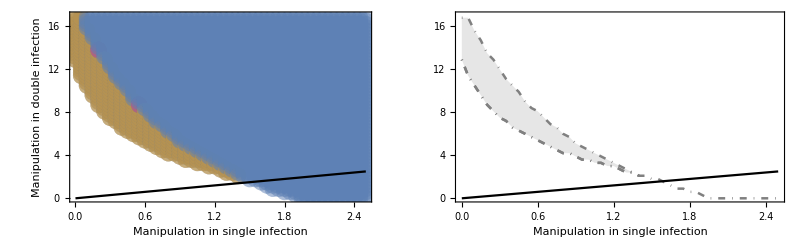

```mathematica
range
equilibrium =eq/. Flatten[manipAllResults2 , 2];
parslist = β/.Flatten[manipAllResults2, 2];
marklist = ListStableMarkTwoParameters[Jmatfunc1/.fww-> ϵ fw, parmanip2,{βw, βww}, parslist, equilibrium, colorstable, True];
MakeListPlotData[parslist[[All, 1]], parslist[[All, 2]]];
p0 = ListPlot[%,  PlotStyle->marklist, PlotRange->range, ImageSize->imageSize, Frame-> includeFrame, FrameLabel->{"Manipulation in single infection", "Manipulation in double infection"},  LabelStyle->labelStyle];
p1 = Plot[x, {x, βwstart, βwend}, PlotStyle-> Black];
pp2 = Show[{p0, p1}];
GetBoundaryLineBiStable[parslist];
lp1 =ListLinePlot[%,  PlotRange->range, Frame->includeFrame, FrameStyle->frameStyle, FrameLabel->{"Manipulation in single infection", ""},  LabelStyle->labelStyle,PlotStyle-> {{Thickness[thick], colbifur[[3]], DotDashed}, {Thickness[thick], colbifur[[3]], DotDashed}}, Filling-> {1-> {2}},FillingStyle->colbifurfilling[[3]], ImageSize->imageSize];
GetBoundaryLineSingle[parslist];
lp2 = ListLinePlot[%,  PlotRange->range, Frame->includeFrame, FrameStyle->frameStyle, LabelStyle->labelStyle, PlotStyle-> {DotDashed,Thickness[thick], colbifur[[3]]}];
l22 = Show[{lp1,lp2, p1}];
GraphicsGrid[{{pp2, l22}}]
```

## Parameter set 3 (f_ww = 0.5 f_w)

CALCULATE

```mathematica
parmanip3 = {ρ -> 1.2, d -> 0.9,r -> 2.5, γ -> 2.9, αw-> 0,αww-> 0, p-> 0.1, c-> 1.4, μ-> 3.9, σw-> 0,σww-> 0,q-> 0.01, δ-> 0.9, k -> 0.26, ϵ-> 0.5, fw -> 36};

manipAllResults3 = ParallelTable[NSolveCodim2Positive[sysfunc1/.fww-> ϵ fw, parmanip3, {βw -> x}, {βww-> y}, β, eq,varRes, 15],{x, βwstart, βwend, βwstep}, {y, βwwstart, βwwend, βwwstep}];
```

NSolve::sfail: Subsystem could not be solved for (172209 Ds)/183067-(117425 Dw)/183067-(116690 Dww)/183067-(138285 Is)/183067+(169206 Iw)/183067-(151916 Iww)/183067-(185189 W)/183067 at value -1.8594951056735897329. The likely cause is failure to detect zero due to low precision. The likely effect is the loss of one or more solutions. Increasing WorkingPrecision might prevent some solutions from being lost.

NSolve::sfail: Subsystem could not be solved for (172209 Ds)/183067-(117425 Dw)/183067-(116690 Dww)/183067-(138285 Is)/183067+(169206 Iw)/183067-(151916 Iww)/183067-(185189 W)/183067 at value 4.333679308414847998. The likely cause is failure to detect zero due to low precision. The likely effect is the loss of one or more solutions. Increasing WorkingPrecision might prevent some solutions from being lost.

PLOT

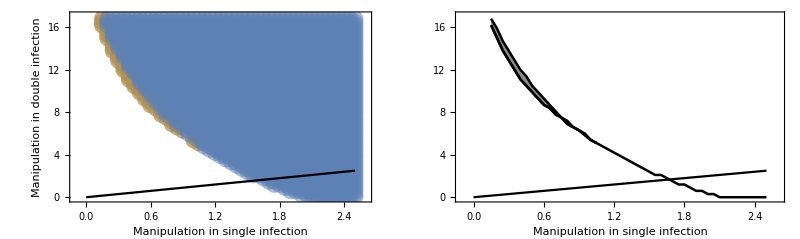

```mathematica
equilibrium =eq/. Flatten[manipAllResults3 , 2];
parslist = β/.Flatten[manipAllResults3, 2];
marklist = ListStableMarkTwoParameters[Jmatfunc1/.fww-> ϵ fw, parmanip3,{βw, βww}, parslist, equilibrium, colorstable, True];
MakeListPlotData[parslist[[All, 1]], parslist[[All, 2]]];
p0 = ListPlot[%,  PlotStyle->marklist, PlotRange->range, ImageSize->imageSize, Frame-> includeFrame, FrameLabel->{"Manipulation in single infection", "Manipulation in double infection"},  LabelStyle->labelStyle];
p1 = Plot[x, {x, βwstart, βwend}, PlotStyle-> Black];
pp2 = Show[{p0, p1}];
GetBoundaryLineBiStable[parslist];
lp1 =ListLinePlot[%,  PlotRange->range, Frame->includeFrame, FrameStyle->frameStyle, FrameLabel->{"Manipulation in single infection", ""},LabelStyle->labelStyle, PlotStyle->{ {Thickness[thick], colbifur[[1]]}, {Thickness[thick], colbifur[[1]]}}, Filling-> {1-> {2}}, FillingStyle->colbifurfilling[[1]], ImageSize->imageSize];
GetBoundaryLineSingle[parslist];
lp2 = ListLinePlot[%,  PlotRange->range, Frame->includeFrame, FrameStyle->frameStyle, LabelStyle->labelStyle, PlotStyle-> {Thickness[thick], colbifur[[1]]}, FrameLabel->"p = 0.1, q = 0.01"];
l23 = Show[{lp1,lp2, p1}];
GraphicsGrid[{{pp2, l23}}]
```

## Combined plots

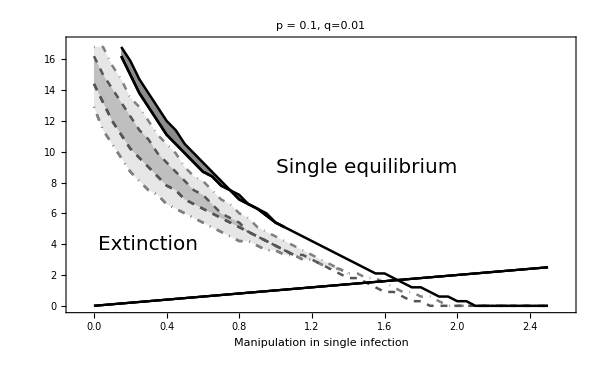

```mathematica
customizeLegend = SwatchLegend[colbifurfilling,{"f_ww = 0.5f_w","f_ww = f_w","f_ww = 2f_w"}, LegendMarkers->{Graphics[{EdgeForm[{Thickness[0.05], Black, Opacity[1]}],Rectangle[]}],Graphics[{EdgeForm[{Dashed, Black, Thickness[0.1], Opacity[0.5]}],Rectangle[]}], Graphics[{EdgeForm[{DotDashed, Black, Thickness[0.1], Opacity[0.3]}],Rectangle[]}]}, LabelStyle->{FontSize-> 14}, LegendMarkerSize->20];
cbp1 = Show[{l22,l21,l23},PlotLabel->"p = 0.1, q=0.01",
	 Epilog->{ Inset[
	Framed[
		customizeLegend
		] ,
	{2.15, 13.9}
				],
			Text[Style["Extinction", FontSize->20], {0.3, 4}],
			 Text[Style["Single equilibrium", FontSize->20], {1.5, 9}]}]
```

## Bifurcation of single and double infection (β_w and β_ww) with higher coinfection from parasite pool to intermediate host

## Parameter set 1 (f_ww= f_w)

CALCULATION

```mathematica
βwstart = 0;
βwend = 2.5;
βwstep = 0.05;
βwwstart = 0;
βwwend = 2.5;
βwwstep = 0.05;

parmanipHcoin1 = {ρ -> 1.2, d -> 0.9,r -> 2.5, γ -> 2.9, αw-> 0,αww-> 0, p-> 0.5, c-> 1.4, μ-> 3.9, σw-> 0,σww-> 0,q-> 0.01, δ-> 0.9, k -> 0.26, ϵ-> 1, fw -> 40};

manipHcoinAllResults1 = ParallelTable[NSolveCodim2Positive[sysfunc1/.fww-> ϵ fw, parmanipHcoin1, {βw -> x}, {βww-> y}, β, eq,varRes, 15],{x, βwstart, βwend, βwstep}, {y, βwwstart, βwwend, βwwstep}];
```

PLOT

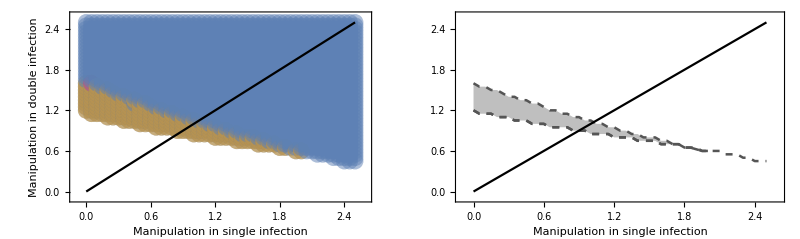

```mathematica
βwstart = 0;
βwend = 2.5;
βwstep = 0.05;
βwwstart = 0;
βwwend = 2.5;
βwwstep = 0.05;

equilibrium =eq/. Flatten[manipHcoinAllResults1 , 2];
parslist = β/.Flatten[manipHcoinAllResults1, 2];
range= {{βwstart-0.1, βwend + 0.1}, {βwwstart-0.1, βwwend + 0.1}};

marklist = ListStableMarkTwoParameters[Jmatfunc1/.fww-> ϵ fw, parmanipHcoin1,{βw, βww}, parslist, equilibrium, colorstable, True];
MakeListPlotData[parslist[[All, 1]], parslist[[All, 2]]];
p0 = ListPlot[%,  PlotStyle->marklist, PlotRange->range, ImageSize->imageSize, Frame-> includeFrame, FrameLabel->{"Manipulation in single infection", "Manipulation in double infection"}, LabelStyle->labelStyle];
p1 = Plot[x, {x, βwstart, βwend}, PlotStyle->Black];
pp2 = Show[{p0, p1}];
GetBoundaryLineBiStable[parslist];
lp1 =ListLinePlot[%,  PlotRange->range, Frame->includeFrame, FrameStyle->frameStyle, FrameLabel->{"Manipulation in single infection", ""}, LabelStyle->labelStyle,PlotStyle->  {{Dashed, Thickness[thick], colbifur[[2]]},{Dashed,Thickness[thick], colbifur[[2]]}}, Filling-> {1-> {2}}, FillingStyle->colbifurfilling[[2]],  ImageSize->imageSize];
GetBoundaryLineSingle[parslist];
lp2= ListLinePlot[%, AspectRatio->1, PlotRange->range, Frame->includeFrame, FrameStyle->frameStyle, LabelStyle->labelStyle, PlotStyle->  {{Dashed, Thickness[thick], colbifur[[2]]},{Dashed,Thickness[thick], colbifur[[2]]}}];
lHC21 = Show[{lp1,lp2, p1}];
GraphicsGrid[{{pp2, lHC21}}]
```

## Parameter set 2 (f_ww = 2 f_w)

CALCULATION

```mathematica
βwstart = 0;
βwend = 2.5;
βwstep = 0.05;
βwwstart = 0;
βwwend = 2.5;
βwwstep = 0.05;

parmanipHcoin2= {ρ -> 1.2, d -> 0.9,r -> 2.5, γ -> 2.9, αw-> 0,αww-> 0, p-> 0.5, c-> 1.4, μ-> 3.9, σw-> 0,σww-> 0,q-> 0.01, δ-> 0.9, k -> 0.26, ϵ-> 2, fw -> 40};

manipHcoinAllResults2 = ParallelTable[NSolveCodim2Positive[sysfunc1/.fww-> ϵ fw, parmanipHcoin2, {βw -> x}, {βww-> y}, β, eq,varRes, 15],{x, βwstart, βwend, βwstep}, {y, βwwstart, βwwend, βwwstep}];
```

PLOT

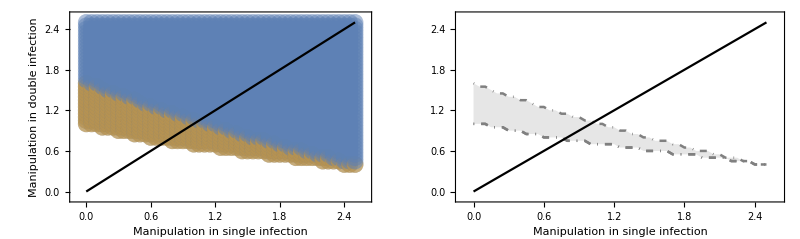

```mathematica
βwstart = 0;
βwend = 2.5;
βwstep = 0.05;
βwwstart = 0;
βwwend = 2.5;
βwwstep = 0.05;

equilibrium =eq/. Flatten[manipHcoinAllResults2 , 2];
parslist = β/.Flatten[manipHcoinAllResults2, 2];
range= {{βwstart-0.1, βwend + 0.1}, {βwwstart-0.1, βwwend + 0.1}};

marklist = ListStableMarkTwoParameters[Jmatfunc1/.fww-> ϵ fw, parmanipHcoin2,{βw, βww}, parslist, equilibrium, colorstable, True];
MakeListPlotData[parslist[[All, 1]], parslist[[All, 2]]];
p0 = ListPlot[%,  PlotStyle->marklist, PlotRange->range, ImageSize->imageSize, Frame-> includeFrame, FrameLabel->{"Manipulation in single infection", "Manipulation in double infection"}, LabelStyle->labelStyle];
p1 = Plot[x, {x, βwstart, βwend}, PlotStyle->Black, AspectRatio->1];
pp2 = Show[{p0, p1}];
GetBoundaryLineBiStable[parslist];
lp1 =ListLinePlot[%,  PlotRange->range, Frame->includeFrame, FrameStyle->frameStyle, FrameLabel->{"Manipulation in single infection", ""}, LabelStyle->labelStyle, PlotStyle-> {{DotDashed,Thickness[thick], colbifur[[3]]}, {DotDashed,Thickness[thick], colbifur[[3]]}}, Filling-> {1-> {2}},  FillingStyle-> colbifurfilling[[3]],ImageSize->imageSize];
GetBoundaryLineSingle[parslist];
lp2= ListLinePlot[%,  PlotRange->range, Frame->includeFrame, FrameStyle->frameStyle, LabelStyle->labelStyle, PlotStyle-> {DotDashed,Thickness[thick], colbifur[[3]]}];
lHC22 = Show[{lp1,lp2, p1}];
GraphicsGrid[{{pp2, lHC22}}]
```

## Parameter set 3 (f_ww = 0.5 f_w)

```mathematica
βwstart = 0;
βwend = 2.5;
βwstep = 0.05;
βwwstart = 0;
βwwend = 2.5;
βwwstep = 0.05;

parmanipHcoin3= {ρ -> 1.2, d -> 0.9,r -> 2.5, γ -> 2.9, αw-> 0,αww-> 0, p-> 0.5, c-> 1.4, μ-> 3.9, σw-> 0,σww-> 0,q-> 0.01, δ-> 0.9, k -> 0.26, ϵ-> 0.5, fw -> 40};

manipHcoinAllResults3 = ParallelTable[NSolveCodim2Positive[sysfunc1/.fww-> ϵ fw, parmanipHcoin3, {βw -> x}, {βww-> y}, β, eq,varRes, 15],{x, βwstart, βwend, βwstep}, {y, βwwstart, βwwend, βwwstep}];
```

PLOT

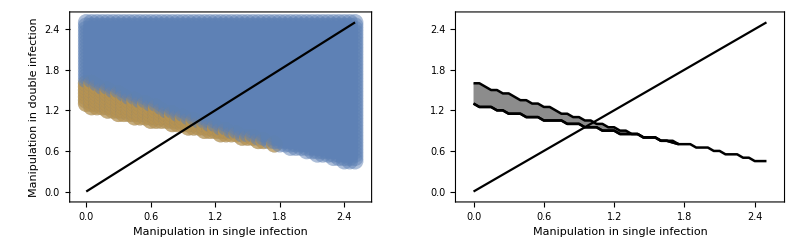

```mathematica
βwstart = 0;
βwend = 2.5;
βwstep = 0.05;
βwwstart = 0;
βwwend = 2.5;
βwwstep = 0.05;

equilibrium =eq/. Flatten[manipHcoinAllResults3, 2];
parslist = β/.Flatten[manipHcoinAllResults3, 2];
range= {{βwstart-0.1, βwend + 0.1}, {βwwstart-0.1, βwwend + 0.1}};


marklist = ListStableMarkTwoParameters[Jmatfunc1/.fww-> ϵ fw, parmanipHcoin3,{βw, βww}, parslist, equilibrium, colorstable, True];
MakeListPlotData[parslist[[All, 1]], parslist[[All, 2]]];
p0 = ListPlot[%,  PlotStyle->marklist, PlotRange->range, ImageSize->imageSize, Frame-> includeFrame, FrameLabel->{"Manipulation in single infection", "Manipulation in double infection"}, LabelStyle->labelStyle];
p1 = Plot[x, {x, βwstart, βwend}, PlotStyle->Black];
pp3 = Show[{p0, p1}];
GetBoundaryLineBiStable[parslist];
lp1 =ListLinePlot[%,  PlotRange->range, Frame->includeFrame, FrameStyle->frameStyle, FrameLabel->{ "Manipulation in single infection", ""},  LabelStyle->labelStyle,PlotStyle-> {{Thickness[thick], colbifur[[1]]}, {Thickness[thick], colbifur[[1]]}}, Filling-> {1-> {2}}, FillingStyle->colbifurfilling[[1]], ImageSize->imageSize];
GetBoundaryLineSingle[parslist];
lp2= ListLinePlot[%,  PlotRange->range, Frame->includeFrame, FrameStyle->frameStyle, LabelStyle->labelStyle, PlotStyle-> {Thickness[thick], colbifur[[1]]}];
lHC23 = Show[{lp1,lp2, p1}];
GraphicsGrid[{{pp3, lHC23}}]
```

## Combined plot

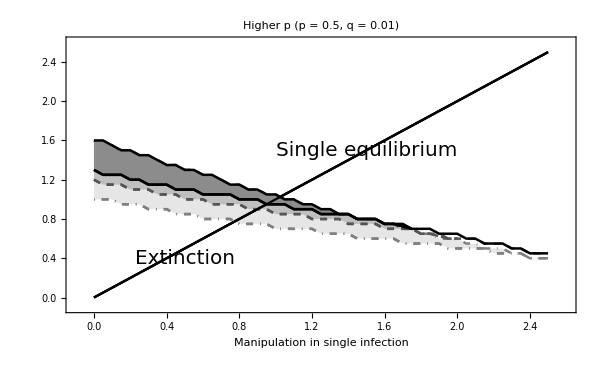

```mathematica
cbp2 = Show[{lHC22, lHC21, lHC23 },PlotLabel-> "Higher p (p = 0.5, q = 0.01)",
	 Epilog->{ Text[Style["Extinction", FontSize->20], {0.5, 0.4}],
			Text[Style["Single equilibrium", FontSize->20], {1.5, 1.5}]}]
```

## Manipulation bifurcation graph when coinfection from intermediate to definitive host is high

## Parameter set 1 (f_ww= f_w)

CALCULATE

```mathematica
thick = 0.003;
βwstart = 0;
βwend = 2.5;
βwstep = 0.05;
βwwstart = 0;
βwwend = 17;
βwwstep = 0.4;

parmanipHcoin4 = {ρ -> 1.2, d -> 0.9,r -> 2.5, γ -> 2.9, αw-> 0,αww-> 0, p-> 0.1, c-> 1.4, μ-> 3.9, σw-> 0,σww-> 0,q-> 0.3, δ-> 0.9, k -> 0.26, ϵ-> 1, fw -> 40};

manipHcoinAllResults4 = ParallelTable[NSolveCodim2Positive[sysfunc1/.fww-> ϵ fw, parmanipHcoin4, {βw -> x}, {βww-> y}, β, eq,varRes, 12],{x, βwstart, βwend, βwstep}, {y, βwwstart, βwwend, βwwstep}];
```

$Aborted

PLOT

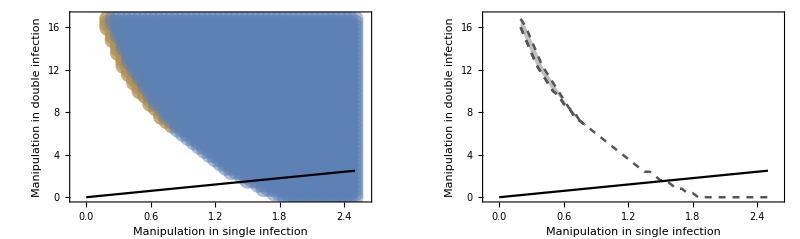

```mathematica
thick = 0.003;
βwstart = 0;
βwend = 2.5;
βwstep = 0.05;
βwwstart = 0;
βwwend = 17;
βwwstep = 0.4;

equilibrium =eq/. Flatten[manipHcoinAllResults4 , 2];
parslist = β/.Flatten[manipHcoinAllResults4, 2];
range= {{βwstart-0.1, βwend + 0.1}, {βwwstart-0.1, βwwend + 0.1}};

marklist = ListStableMarkTwoParameters[Jmatfunc1/.fww-> ϵ fw, parmanipHcoin4,{βw, βww}, parslist, equilibrium, colorstable, True];
MakeListPlotData[parslist[[All, 1]], parslist[[All, 2]]];
p0 = ListPlot[%,  PlotStyle->marklist, PlotRange->range, ImageSize->imageSize, Frame-> includeFrame, FrameLabel->{"Manipulation in single infection", "Manipulation in double infection"}, LabelStyle->labelStyle];
p1 = Plot[x, {x, βwstart, βwend}, PlotStyle->Black, AspectRatio->1];
pp2 = Show[{p0, p1}];
GetBoundaryLineBiStable[parslist];
lp1 =ListLinePlot[%,  PlotRange->range, Frame->includeFrame, FrameStyle->frameStyle, FrameLabel->{"Manipulation in single infection", "Manipulation in double infection"}, PlotStyle->  {{Dashed, Thickness[thick], colbifur[[2]]},{Dashed,Thickness[thick], colbifur[[2]]}}, Filling-> {1-> {2}}, FillingStyle->colbifurfilling[[2]],LabelStyle->labelStyle, ImageSize->imageSize];
GetBoundaryLineSingle[parslist];
lp2= ListLinePlot[%, AspectRatio->1, PlotRange->range, Frame->includeFrame, FrameStyle->frameStyle, LabelStyle->labelStyle, PlotStyle->  {{Dashed, Thickness[thick], colbifur[[2]]},{Dashed,Thickness[thick], colbifur[[2]]}}];
lHCq21 = Show[{lp1,lp2, p1}];
GraphicsGrid[{{pp2, lHCq21}}]
```

## Parameter set 2 (fww = 2 fw)

CALCULATE

```mathematica
thick = 0.003;
βwstart = 0;
βwend = 2.5;
βwstep = 0.05;
βwwstart = 0;
βwwend = 17;
βwwstep = 0.4;

parmanipHcoin5 = {ρ -> 1.2, d -> 0.9,r -> 2.5, γ -> 2.9, αw-> 0,αww-> 0, p-> 0.1, c-> 1.4, μ-> 3.9, σw-> 0,σww-> 0,q-> 0.3, δ-> 0.9, k -> 0.26, ϵ-> 2, fw -> 40};

manipHcoinAllResults5 = ParallelTable[NSolveCodim2Positive[sysfunc1/.fww-> ϵ fw, parmanipHcoin5, {βw -> x}, {βww-> y}, β, eq,varRes, 15],{x, βwstart, βwend, βwstep}, {y, βwwstart, βwwend, βwwstep}];
```

PLOT

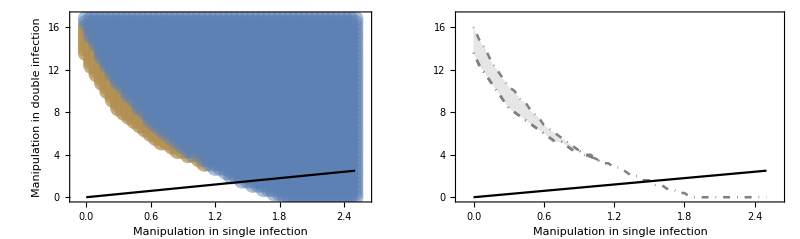

```mathematica
thick = 0.003;
βwstart = 0;
βwend = 2.5;
βwstep = 0.05;
βwwstart = 0;
βwwend = 17;
βwwstep = 0.4;

equilibrium =eq/. Flatten[manipHcoinAllResults5 , 2];
parslist = β/.Flatten[manipHcoinAllResults5, 2];
range= {{βwstart-0.1, βwend + 0.1}, {βwwstart-0.1, βwwend + 0.1}};

marklist = ListStableMarkTwoParameters[Jmatfunc1/.fww-> ϵ fw, parmanipHcoin5,{βw, βww}, parslist, equilibrium, colorstable, True];
MakeListPlotData[parslist[[All, 1]], parslist[[All, 2]]];
p0 = ListPlot[%,  PlotStyle->marklist, PlotRange->range, ImageSize->imageSize, Frame-> includeFrame, FrameLabel->{"Manipulation in single infection", "Manipulation in double infection"}, LabelStyle->labelStyle];
p1 = Plot[x, {x, βwstart, βwend}, PlotStyle->Black];
pp2 = Show[{p0, p1}];
GetBoundaryLineBiStable[parslist];
lp1 =ListLinePlot[%,  PlotRange->range, Frame->includeFrame, FrameStyle->frameStyle, FrameLabel->{"Manipulation in single infection", ""}, LabelStyle->labelStyle, PlotStyle-> {{DotDashed,Thickness[thick], colbifur[[3]]}, {DotDashed,Thickness[thick], colbifur[[3]]}}, Filling-> {1-> {2}}, FillingStyle->colbifurfilling[[3]],ImageSize->imageSize];
GetBoundaryLineSingle[parslist];
lp2= ListLinePlot[%, PlotRange->range, Frame->includeFrame, FrameStyle->frameStyle, LabelStyle->labelStyle, PlotStyle-> {DotDashed,Thickness[thick], colbifur[[3]]}];
lHCq22 = Show[{lp1,lp2, p1}];
GraphicsGrid[{{pp2, lHCq22}}]
```

## Parameter set 3 (fww = 0.5 fw)

CALCULATE

```mathematica
thick = 0.003;
βwstart = 0;
βwend = 2.5;
βwstep = 0.05;
βwwstart = 0;
βwwend = 17;
βwwstep = 0.4;

parmanipHcoin6 = {ρ -> 1.2, d -> 0.9,r -> 2.5, γ -> 2.9, αw-> 0,αww-> 0, p-> 0.1, c-> 1.4, μ-> 3.9, σw-> 0,σww-> 0,q-> 0.3, δ-> 0.9, k -> 0.26, ϵ-> 0.5, fw -> 40};

manipHcoinAllResults6 = ParallelTable[NSolveCodim2Positive[sysfunc1/.fww-> ϵ fw, parmanipHcoin6, {βw -> x}, {βww-> y}, β, eq,varRes, 15],{x, βwstart, βwend, βwstep}, {y, βwwstart, βwwend, βwwstep}];
```

PLOT

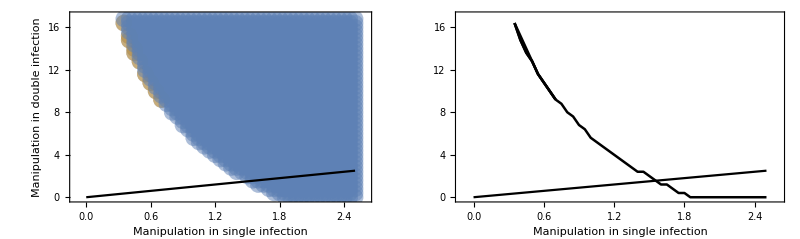

```mathematica
thick = 0.003;
βwstart = 0;
βwend = 2.5;
βwstep = 0.05;
βwwstart = 0;
βwwend = 17;
βwwstep = 0.4;

equilibrium =eq/. Flatten[manipHcoinAllResults6, 2];
parslist = β/.Flatten[manipHcoinAllResults6, 2];
range= {{βwstart-0.1, βwend + 0.1}, {βwwstart-0.1, βwwend + 0.1}};


marklist = ListStableMarkTwoParameters[Jmatfunc1/.fww-> ϵ fw, parmanipHcoin6,{βw, βww}, parslist, equilibrium, colorstable, True];
MakeListPlotData[parslist[[All, 1]], parslist[[All, 2]]];
p0 = ListPlot[%,  PlotStyle->marklist, PlotRange->range, ImageSize->imageSize, Frame-> includeFrame, FrameLabel->{"Manipulation in single infection", "Manipulation in double infection"}, LabelStyle->labelStyle];
p1 = Plot[x, {x, βwstart, βwend}, PlotStyle->Black];
pp3 = Show[{p0, p1}];
GetBoundaryLineBiStable[parslist];
lp1 =ListLinePlot[%,  PlotRange->range, Frame->includeFrame, FrameStyle->frameStyle, FrameLabel->{"Manipulation in single infection", ""}, LabelStyle->labelStyle,PlotStyle-> {{Thickness[thick], colbifur[[1]]}, {Thickness[thick], colbifur[[1]]}}, Filling-> {1-> {2}},FillingStyle->colbifurfilling[[1]],  ImageSize->imageSize];
GetBoundaryLineSingle[parslist];
lp2= ListLinePlot[%, PlotRange->range, Frame->includeFrame, FrameStyle->frameStyle, LabelStyle->labelStyle, PlotStyle-> {Thickness[thick], colbifur[[1]]}];
lHCq23 = Show[{lp1,lp2, p1}];
GraphicsGrid[{{pp3, lHCq23}}]
```

## Combined plot

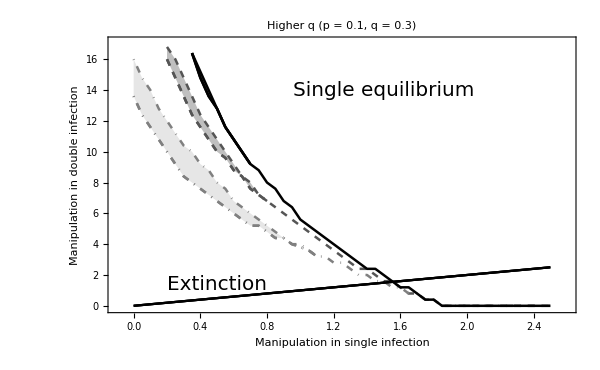

```mathematica
cbp3 = Show[{lHCq21, lHCq22, lHCq23 },PlotLabel-> "Higher q (p = 0.1, q = 0.3)",
	 Epilog->{ Text[Style["Extinction", FontSize->20], {0.5, 1.4}],
			Text[Style["Single equilibrium", FontSize->20], {1.5, 14}], Arrow[{{1,18},{1.5,18}}]}]
```

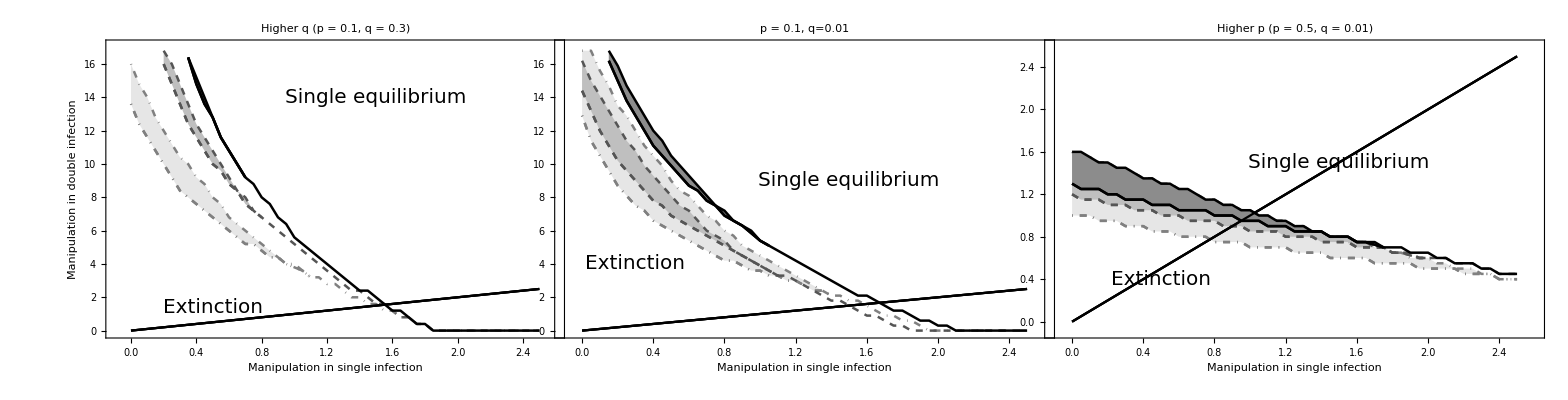

manip_bifurcation.pdf

```mathematica
Size = {1600, 400};
GraphicsRow[{ cbp3,cbp1, cbp2}, ImageSize->Size, Spacings->-100]
(*Export["manip_bifurcation.pdf",%, ImageResolution-> figResolution]*)
```